```mathematica
plotBuffer[path_,opts:OptionsPattern[]]:=Module[{file,headings,points},
file=Import[path];
headings=file//First;
points=file//Rest;
data=Most[points]//Transpose;
Print[Join[{headings},Take[points,-10]]//TableForm];
Print["Total # of particles: ",points⟦-2⟧//Total];
ListLinePlot[
data,
PlotLegends->headings,
AxesLabel->{"timestep","Number of particles"},
DataRange->{0,(Length[data//Transpose])*10},
GridLines->Automatic,
opts
]
]
```

```mathematica
plotBuffer["D:\\measureBuffer\\countCells.csv"]
```

nPellets | nBuffer | nEnergy | nCells
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22607 | 71804 | 5580 | 9
22616 | 71804 | 5580 | 0

Total # of particles: 100000

-Graphics-

```mathematica
Export["D:\\measureBuffer 3\\bufferplot 3.png",%217,ImageResolution->300]
```

D:\measureBuffer 3\bufferplot 3.png

nDetritus | nBuffer | nEnergy | nCells
17288 | 15228 | 30000 | 47484
17277 | 15231 | 30000 | 47492
17270 | 15254 | 30000 | 47476
17264 | 15279 | 30000 | 47457
17257 | 15240 | 30000 | 47503
17247 | 15245 | 30000 | 47508
17246 | 15248 | 30000 | 47506
17242 | 15275 | 30000 | 47483
17242 | 15274 | 30000 | 47484
17227 | 15280 | 30000 | 47493

Total # of particles: 110000

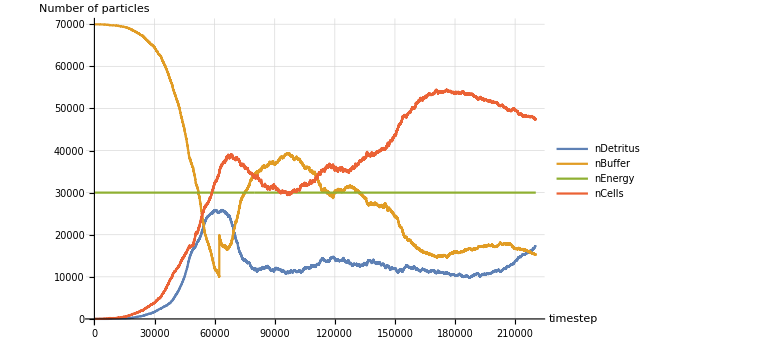

```mathematica
plotBuffer["D:\\measureBuffer 3\\countCells.csv",ImageSize->Large]
```

```mathematica
plotBuffer["D:\\workingBuffer\\countCells.csv",ImageSize->Large]
```

nDetritus | nBuffer | nEnergy | nCells
16320 | 73658 | 30000 | 22
16320 | 73658 | 30000 | 22
16319 | 73659 | 30000 | 22
16319 | 73659 | 30000 | 22
16318 | 73660 | 30000 | 22
16317 | 73661 | 30000 | 22
16317 | 73661 | 30000 | 22
16317 | 73661 | 30000 | 22
16317 | 73661 | 30000 | 22
16316 | 73662 | 30000 | 22

Total # of particles: 120000

-Graphics-

```mathematica
plotBuffer["D:\\betterEnergy 2\\countCells.csv",ImageSize->Large,PlotRange->Full]
```

nDetritus | nBuffer | nEnergy | nCells
5856 | 57926 | 15000 | 24
5855 | 57927 | 15000 | 24
5855 | 57927 | 15000 | 24
5855 | 57927 | 15000 | 24
5855 | 57927 | 15000 | 24
5854 | 57928 | 15000 | 24
5854 | 57928 | 15000 | 24
5854 | 57928 | 15000 | 24
5854 | 57928 | 15000 | 24
5854 | 57928 | 15000 | 24

Total # of particles: 78806

-Graphics-

```mathematica
plotBuffer["D:\\betterEnergy 3\\countCells.csv",ImageSize->Large,PlotRange->Full]
```

nDetritus | nBuffer | nEnergy | nCells
850 | 40665 | 15000 | 24
849 | 40666 | 15000 | 24
849 | 40666 | 15000 | 24
849 | 40666 | 15000 | 24
848 | 40667 | 15000 | 24
848 | 40667 | 15000 | 24
848 | 40667 | 15000 | 24
848 | 40667 | 15000 | 24
848 | 40667 | 15000 | 24
848 | 40667 | 15000 | 24

Total # of particles: 56539

-Graphics-

```mathematica
plotBuffer["D:\\monitorParticle\\countCells.csv",ImageSize->Large,PlotRange->Full]
```

nDetritus | nBuffer | nEnergy | nCells
922 | 20631 | 15000 | 752
921 | 20632 | 15000 | 752
921 | 20632 | 15000 | 752
920 | 20633 | 15000 | 752
919 | 20634 | 15000 | 752
917 | 20636 | 15000 | 752
917 | 20636 | 15000 | 752
916 | 20637 | 15000 | 752
915 | 20638 | 15000 | 752
914 |  |  |

Total # of particles: 37305

-Graphics-